# Primer examen de Métodos numéricos Nombre:Fernando Angel Medellín Cuevas

## Programas usados en el examen

```mathematica
$PrePrint=TraditionalForm
```

TraditionalForm

```mathematica
(*biseccion*)
(*llamamos a la funcion bisec que espera la funcion y 2 valores a y b. como esperamos un resultado se le asigna a1 y b1, n es cuandtas iteraciones va a hacer, pre el número de sifras significativas*)
bisec[f_,a1_,b1_,n_,pre_]:=Module[{a = SetPrecision[ a1,pre],b=SetPrecision[ b1,pre]},
(*en la lista de la función que va a evaluar para que guarde la cantidad de errores*)
list=Table[c=(a+b)/2;If[(f/.x->c)(f/.x->b)<0,a=c,b=c],{n}];
(*funcion para sacar el error absoluto y el error relativo
error absoluto es el valor real-valor aprox
error relativo (val real-val aprox)/(Val real)*)
error=Abs[list[[n]]-list[[n-1]]]/list[[n]];{c,error}
]
```

## 1- (6.15)

-0.822423/(x (x+0.00186262))+120.772/(x-0.00186262)-65

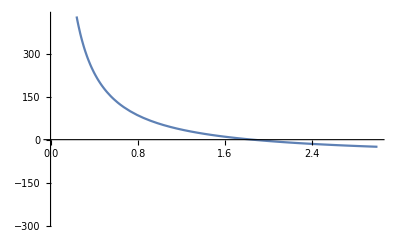

```mathematica
(*Utilizando el método de bisección*)
(*Datos del programa*)
R=0.518;
T=233.15;
Pc=4600;
P=65;
Tc=191;
(*ecuaciones de a y b*)
a=0.427(R^2 Tc^2.5)/Pc;
b= 0.0866 R Tc/Pc;
(*Despeje de la función y sustituir por x*)
f= (R T)/(x-b)-a/(x(x+b)√T)-P
Plot[f,{x,0,3}]
```

```mathematica
bisec[f,1.5,1.9,10,10][[1]]
```

1.852734375

```mathematica
vol=3/(bisec[f,0,3,10,10][[1]]) (*dato la masa es de 3 m^3 para calcular es m^3/(kg (este es el resultado de bisección))*)
```

1.617693523

## 2 - (6.17)

-x/10+1/10 x cosh(500/x)-10

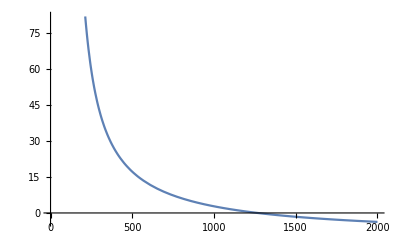

```mathematica
w=10;
y0=5;
y=15;
x1=50;
fun617=x/w Cosh[w/x x1]+y0-x/w-y

Plot[fun617,{x,0,2000}]
```

```mathematica
bisec[fun617,0,2000,20,20][[1]]
```

1266.3249969482421875

(-50 | 0.0019073486328125
-30 | 0.0019073486328125
-10 | 0.0019073486328125
10 | 0.0019073486328125
30 | 537.1608734130859375
50 | 333.7688446044921875
70 | 259.6111297607421875
90 | 221.2924957275390625)

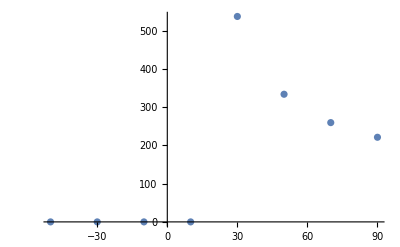

```mathematica
lista=Table[fun617=x/w Cosh[w/x x1]+y0-x/w-y;
{y,bisec[fun617,0,2000,20,20][[1]]},{y,-50,100,20}]
ListPlot[lista]
```

## 3 - (6.21)

90 tan(x)-44.145 sec^2(x)+0.8

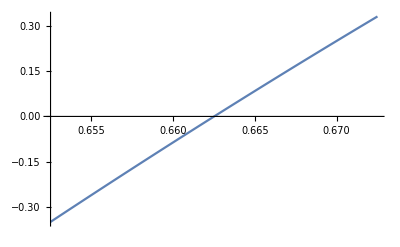

```mathematica
v0=30;
y0=1.8;
y=1;
d=90;
fun621= Tan[x]d-9.81/(2 v0^2(Cos[x])^2)d^2+y0-1
Plot[fun621,{x,0.6525,0.6725}]
```

```mathematica
bisec[fun621,0.6525,0.6725,10,10][[1]]
```

0.6625195312

## 4 - (Newton-Raphson) Este programa calcula las raíces de una función haciendo uso de la aproximación de la derivada de la función. Sólo requiere una función, una aproximación de la raíz y el número de iteraciones. Use el programa para graficar el valor de la raíz vs. el error porcentual de la raíz. Usa la función-ejemplo que se da.

```mathematica
new[f_,a1_,n_]:=Module[{a=a1},

list=Table[b=a;{a=a-(f/.x->a)/(D[f,x]/.x->a),Abs[(b-a)/a 100]},{n}];
Print[MatrixForm [list]];
ListPlot[list]
]
```

```mathematica
new[Sin[x]-x^2,10.,6]
```

(5.17522
2.38061
1.47317
1.06073
0.906166
0.877734)

TraditionalForm

(5.17522 | 93.2287
2.38061 | 117.39
1.47317 | 61.5981
1.06073 | 38.8827
0.906166 | 17.0565
0.877734 | 3.23925)

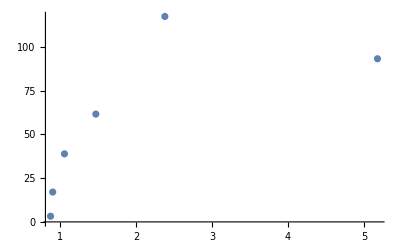

```mathematica
$PrePrint=TraditionalForm
new[Sin[x]-x^2,10.,6]
```

## 5 - (Programa) Hacer un programa que halle los máximos y mínimos y, los puntos silla de una función de dos variables. Corran la función-ejemplo. -Graphics-

```mathematica
Clear[x,y]
```

General::ivar: 1 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

Solve::ivar: 1 is not a valid variable.

ReplaceAll::reps: {∂_1 (-2-9 x-3 x^2+x^3)==0&&-9-6 x+3 x^2==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {x,1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Reals} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 4 of Solve[∂_1 (-2-9 x-3 x^2+x^3)==0&&-9-6 x+3 x^2==0,{x,1},Reals] does not exist.

```mathematica
maxmin[f_]:=Module[{},
(*Sacar derivadas y segundas derivadas*)
dx=D[f,x];
d2x=D[dx,x];
dxy=D[dx,y];
dy=D[f,y];
d2y=D[dy,y];
dyx=D[dy,x];

lista =Table[res={Solve[dy==0&&dx==0,{x,y},Reals]}];

dif=d2x d2y-dyx dxy;
(*Evaluar con funcion igualado a 0*)
v1=dif/.res[[1,1]];
v2=dif/.res[[1,2]];
v3=dif/.res[[1,3]];
v4=dif/.res[[1,4]];
(*puntos críticos*)
val2dx=d2x/. res[[1,1]];
val2dy=d2y/. res[[1,2]];
(* Evaluar maximos minimos y puntos silla*)
If[v1<0,Print["Punto silla en",res[[1,1]]],If[v1>0&&val2dx>0,Print["Punto mínimo",res[[1,1]]],Print["Punto máximo",res[[1,1]]]]];
If[v2<0,Print["Punto silla",res[[1,2]]],If[v2>0&&val2dy>0,Print["Punto mínimo",res[[1,2]]],Print["Punto máximo",res[[1,2]]]]];If[v3<0,Print["Punto silla",res[[1,3]]],If[v3>0&&val2dx>0,Print["Punto mínimo",res[[1,3]]],Print["Punto máximo",res[[1,3]]]]];
If[v4<0,Print["Punto silla",res[[1,4]]],If[v4>0&&val2dy>0,Print["Punto mínimo",res[[1,4]]],Print["Punto máximo",res[[1,4]]]]];
]
```

```mathematica
f=x^3+y^3-3 x^2-3 y^2-9x;
```

```mathematica
maxmin[f]
```

Punto máximo{x→-1,y→0}

Punto silla{x→-1,y→2}

Punto silla{x→3,y→0}

Punto mínimo{x→3,y→2}